```mathematica
m
```

## 第一次

Pressure(mmHg) | Voltage(V) | Current(mA) | Resistance(Ω) | (δQ/dt)_低(W)
0 | 2.07 | 29. | 71.4 | 0
2. | 2.4 | 36.8 | 65.2 | 0.0283
2.5 | 3.87 | 56.3 | 68.7 | 0.158
3. | 3.97 | 57.8 | 68.7 | 0.169
3.5 | 4.07 | 59.3 | 68.6 | 0.181
4. | 4.17 | 60.7 | 68.7 | 0.193
4.5 | 4.25 | 61.7 | 68.9 | 0.202
5. | 4.39 | 62.9 | 69.8 | 0.216
5.5 | 4.38 | 63.6 | 68.9 | 0.219
6. | 4.42 | 64.1 | 69. | 0.223
6.5 | 4.46 | 64.7 | 68.9 | 0.229
7. | 4.49 | 65.1 | 69. | 0.232
7.5 | 4.52 | 65.6 | 68.9 | 0.236
8. | 4.54 | 66. | 68.8 | 0.24
8.5 | 4.56 | 66.2 | 68.9 | 0.242
9. | 4.59 | 66.5 | 69. | 0.245
9.5 | 4.6 | 66.8 | 68.9 | 0.247
10. | 4.62 | 67. | 69. | 0.25

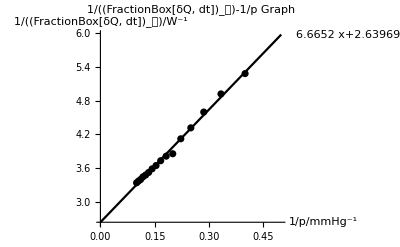

```mathematica
Clear[a,b,c,d,e,x];
f[{a_,b_,c_}]:={a,b,c,SetPrecision[(b*1000)/c,3],SetPrecision[b*c/1000-2.07*29.0/1000,3]};
TableForm[list1=Map[f,list],
TableHeadings->{None,{"Pressure(mmHg)","Voltage(V)","Current(mA)","Resistance(Ω)","(δQ/dt)_(:4f4e)(W)"}}]
list2=Drop[list1,{1,2}];
g[{a_,b_,c_,d_,e_}]:={1/a,1/(1.2*e)};
list3=Map[g,list2];
Fit[list3,{1,x},x];
Show[Plot[%,{x,0,0.5},PlotLabels->%,PlotStyle->Black,PlotLabel->"1/((FractionBox[δQ, dt])_(:4f4e))-1/p  Graph",AxesLabel->{"1/p/mmHg^-1","1/((FractionBox[δQ, dt])_(:4f4e))/W^-1"},LabelStyle->Black],
ListPlot[list3,PlotStyle->Black],ImageSize->Full]
Clear[a,b,c,d,e,x];
```

```mathematica
R=0.997571,1/Q=2.64,Q=0.379,κ=0.379/(0.3*2*Pi)*Log[15.5/0.0224]/((69.0-54.1)/(5.1*10^-3*69.0)-14.0)=0.0464
```

0.997571

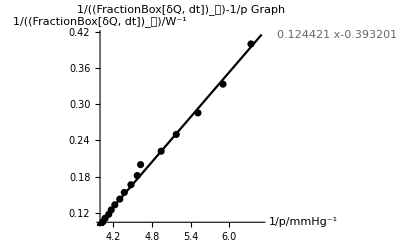

```mathematica
Clear[a,b,c,d,e,f,x];

a=list3;
Average[x_List]:=Total[x]/Count[x,_List];
f[{a_,b_}]:=a*b;
c=(#-Average[a])&/@a;
d=(Map[First,c])^2;
e=(Map[Last,c])^2;
result=Total[Map[f,c]]/Sqrt[Total[d]*Total[e]]

Clear[a,b,c,d,e,f];

Fit[list3,{1,x},x];
Show[Plot[%,{x,4,6.5},PlotLabels->{%,result},PlotStyle->Black,PlotLabel->"1/((FractionBox[δQ, dt])_(:4f4e))-1/p  Graph",AxesLabel->{"1/p/mmHg^-1","1/((FractionBox[δQ, dt])_(:4f4e))/W^-1"}],
ListPlot[list3,PlotStyle->Black]]

Clear[result];
```

```mathematica
Module[
Clear[a,b];
a=1;
b=2;
b+2
```

```mathematica
1/2.63969
```

0.378832

```mathematica
0.379/(0.3*2*Pi)*Log[15.5/0.0224]/((69.0-54.1)/(5.1*10^-3*69.0)-14.0)
```

0.0463939

## 第二次

| v_1/(cm/s) | v_2/(cm/s) | v_1/2 | a/(cm/s^2) | F/(g*cm/s^2)
1 | 25.26 | 24.87 | 25.07 | 0.25 | 48.15
2 | 12.8 | 12.55 | 12.68 | 0.08 | 15.41
3 | 27.85 | 27.34 | 27.59 | 0.36 | 69.33
4 | 39.82 | 39.36 | 39.59 | 0.46 | 88.59
5 | 26.77 | 26.32 | 26.55 | 0.3 | 57.77

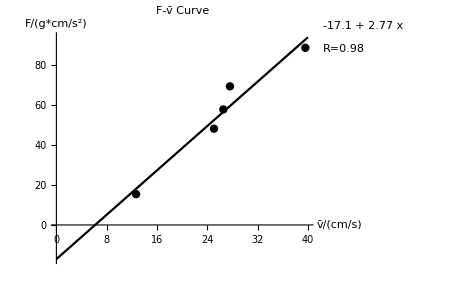

| v_(1, 0) | v_(2, 0) | v_(1, 1) | v_(2, 1) | p_1 | p_2 | E_1 | E_2 | Δp | ΔE | p相对误差 | E相对误差
1 | 17.9 | 26.05 | 21.79 | 14.5 | 1823. | 1180. | 96740. | 64820. | 642.5 | 31920. | 0.353 | 0.33
2 | 23.39 | 27.11 | 25.18 | 20.9 | 1013. | 545.4 | 123300. | 102000. | 467.9 | 21370. | 0.462 | 0.173
3 | 21.46 | 18.2 | 19.06 | 14.38 | 388.2 | 697.2 | 75440. | 54130. | 309. | 21310. | 0.443 | 0.283
4 | 12.43 | 18. | 16.69 | 11.33 | 1248. | 859.8 | 46330. | 38520. | 388.3 | 7807. | 0.311 | 0.169
5 | 15.8 | 17.89 | 15.35 | 13.44 | 600.9 | 194.4 | 54770. | 39700. | 406.5 | 15070. | 0.677 | 0.275

| Δp | ΔE | p相对误差 | E相对误差
1 | 642.5 | 31920. | 0.353 | 0.33
2 | 467.9 | 21370. | 0.462 | 0.173
3 | 309. | 21310. | 0.443 | 0.283
4 | 388.3 | 7807. | 0.311 | 0.169
5 | 406.5 | 15070. | 0.677 | 0.275

| v_(1, 0) | v_(2, 0) | v_(2, 1) | p_1 | p_2 | E_1 | E_2 | Δp | ΔE
1 | 32.67 | 18.36 | 6.37 | 2718. | 2376. | 131300. | 7569. | 341.6 | 123800.
2 | 15.64 | 62.02 | 18.06 | 8577. | 6738. | 379800. | 60840. | 1840. | 319000.
3 | 49.38 | 19.69 | 11.57 | 5604. | 4316. | 264600. | 24970. | 1288. | 239600.
4 | 36.9 | 15.33 | 8.37 | 4073. | 3123. | 149500. | 13070. | 950.8 | 136400.
5 | 32.3 | 15.05 | 6.76 | 3263. | 2522. | 118800. | 8524. | 741. | 110300.

| ΔE
1 | 123800.
2 | 319000.
3 | 239600.
4 | 136400.
5 | 110300.

```mathematica
list1={{25.26,24.87,0.25},{12.80,12.55,0.08},{27.85,27.34,0.36},{39.82,39.36,0.46},{26.77,26.32,0.30}};
list2={{17.90,26.05,21.79,14.50},{23.39,27.11,25.18,20.90},{21.46,18.20,19.06,14.38},{12.43,18.00,16.69,11.33},{15.80,17.89,15.35,13.44}};
list3={{32.67,18.36,6.37},{15.64,62.02,18.06},{49.38,19.69,11.57},{36.90,15.33,8.37},{32.30,15.05,6.76}};
lista=({#[[1]],#[[2]],(#[[1]]+#[[2]])/2,#[[3]],192.58*#[[3]]}&/@list1)~SetPrecision~4;
TableForm[lista,TableHeadings->{Range[5],{"v_1/(cm/s)","v_2/(cm/s)","v_1/2","a/(cm/s^2)","F/(g*cm/s^2)"}}]
Show[LineModelPlot[{#[[3]],#[[5]]}&/@lista,"v̄/(cm/s)","F/(g*cm/s^2)",0,40,"F-v̄ Curve"],ImageSize->Large]
listb=({#[[1]],#[[2]],#[[3]],#[[4]],185.58*#[[1]]-197.49*#[[2]],185.58*#[[3]]-197.49*#[[4]],1/2*185.58*(#[[1]])^2+1/2*197.49*(#[[2]])^2,1/2*185.58*(#[[3]])^2+1/2*197.49*(#[[4]])^2}&/@list2);
listb=(Abs/@#)&/@listb;
listb1=(Flatten[{#,Abs[#[[5]]-#[[6]]],Abs[#[[7]]-#[[8]]]}]&/@listb)~SetPrecision~4;
listb2=Flatten[{#,(#[[9]])/Max[#[[5]],#[[6]]],(#[[10]])/Max[#[[7]],#[[8]]]}]&/@listb1;
listb=TableForm[listb2,TableHeadings->{Range[5],{"v_(1, 0)","v_(2, 0)","v_(1, 1)","v_(2, 1)","p_1","p_2","E_1","E_2","Δp","ΔE","p相对误差","E相对误差"}}]
TableForm[{#[[9]],#[[10]],#[[11]],#[[12]]}&/@listb2,TableHeadings->{Range[5],{"Δp","ΔE","p相对误差","E相对误差"}}]
listc=({#[[1]],#[[2]],#[[3]],187.49*#[[1]]-185.58*#[[2]],(187.49+185.58)*#[[3]],0.5*187.49*(#[[1]])^2+0.5*185.58*(#[[2]])^2,0.5*(187.49+185.58)*(#[[3]])^2}&/@list3);
TableForm[(Flatten[{#,Abs[#[[4]]-#[[5]]],Abs[#[[6]]-#[[7]]]}]&/@((Abs/@#)&/@listc))~SetPrecision~4,TableHeadings->{Range[5],{"v_(1, 0)","v_(2, 0)","v_(2, 1)","p_1","p_2","E_1","E_2","Δp","ΔE"}}]
TableForm[{#[[9]]}&/@((Flatten[{#,Abs[#[[4]]-#[[5]]],Abs[#[[6]]-#[[7]]]}]&/@((Abs/@#)&/@listc))~SetPrecision~4),TableHeadings->{Range[5],{"ΔE"}}]
```

```mathematica
length1={{{14.1,42},{13.9,40},{14.0,41},{14.0,41},{14.1,42}},{{14.6,47},{13.9,40},{14.1,42},{14.4,45},{13.5,36}},{{13.5,42},{9.6,2},{13.8,45},{12.5,32},{12.8,35}},{{14.5,20},{14.8,23},{16.5,40},{15.0,25},{13.1,5}}};T={{0.5532,0.5537,0.5532,0.5531,0.5524},{1.0106,1.0164,1.0131,1.0169,1.0228},{1.1566,1.1615,1.1635,1.1546,1.1575},{1.1251,1.1239,1.1210,1.1173,1.1279},{1.6617,1.6687,1.6649,1.6612,1.6628}};
T2={{5,1.8584},{10,2.3882},{15,3.0506},{20,3.9191},{25,4.6467}};
m1=866.15;m2=671.51;m3=1248.37;m4=131.42;m5=473.85;
m={{m1,m2,m3,m4,m5}};
```

```mathematica
length2=(((10*(#[[1]]-4.9/50*#[[2]])&)/@#&)/@length1)~SetAccuracy~3
```

{{99.84,99.8,99.82,99.82,99.84},{99.94,99.8,99.84,99.9,99.72},{93.84,94.04,93.9,93.64,93.7},{125.4,125.46,125.8,125.5,126.1}}

```mathematica
TableForm[m,TableDirections->Column,TableHeadings->{{"质量/g"},{"圆柱","圆筒","圆球","细杆","小圆筒"}}]
```

| 圆柱 | 圆筒 | 圆球 | 细杆 | 小圆筒
质量/g | 866.15 | 671.51 | 1248.37 | 131.42 | 473.85

```mathematica
TableForm[length/.({#[[4]]->SetPrecision[#[[4]],5],#[[5]]->SetPrecision[#[[5]],4]}&@length),TableHeadings->{{"圆柱直径","圆筒外径","圆筒内径","圆球直径","细杆长度"},{"L_1/mm","L_2/mm","L_3/mm","L_4/mm","L_5/mm","L/mm","绝对误差","不确定度"}}]
```

| L_1/mm | L_2/mm | L_3/mm | L_4/mm | L_5/mm | L/mm | 绝对误差 | 不确定度
圆柱直径 | 99.84 | 99.8 | 99.82 | 99.82 | 99.84 | 99.82 | 0.0148 | 0.0082
圆筒外径 | 99.94 | 99.8 | 99.84 | 99.9 | 99.72 | 99.84 | 0.0769 | 0.043
圆筒内径 | 93.84 | 94.04 | 93.9 | 93.64 | 93.7 | 93.82 | 0.1428 | 0.0798
圆球直径 | 125.4 | 125.46 | 125.8 | 125.5 | 126.1 | 125.65 | 0.26309 | 0.14707
细杆长度 | 610. | 610. | 610.5 | 610. | 610.3 | 610.2 | 0.2059 | 0.1151

```mathematica
t=Flatten/@({#~SetAccuracy~5,Mean[#]~SetAccuracy~5,SetAccuracy[StandardError[#],8],SetAccuracy[StandardUncertaintyA[#],8]}&/@T);
TableForm[t,TableHeadings->{{"圆盘","圆柱","圆筒","圆球","细杆"},{"T_1/s","T_2/s","T_3/s","T_4/s","T_5/s","T/s","绝对误差","不确定度"}}]
```

| T_1/s | T_2/s | T_3/s | T_4/s | T_5/s | T/s | 绝对误差 | 不确定度
圆盘 | 0.5532 | 0.5537 | 0.5532 | 0.5531 | 0.5524 | 0.5531 | 0.0004167 | 0.0002329
圆柱 | 1.0106 | 1.0164 | 1.0131 | 1.0169 | 1.0228 | 1.016 | 0.0041176 | 0.0023018
圆筒 | 1.1566 | 1.1615 | 1.1635 | 1.1546 | 1.1575 | 1.1587 | 0.0032721 | 0.0018291
圆球 | 1.1251 | 1.1239 | 1.121 | 1.1173 | 1.1279 | 1.123 | 0.0036252 | 0.0020266
细杆 | 1.6617 | 1.6687 | 1.6649 | 1.6612 | 1.6628 | 1.6639 | 0.0027339 | 0.0015283

```mathematica
TableForm[{{k,(k*(t[[1]][[6]])^2)/(4*Pi^2)  }},TableHeadings->{None,{"K/(g×cm^2/s^2)","I_0/(g×cm^2)"}}]
```

K/(g×cm^2/s^2) | I_0/(g×cm^2)
586485. | 4545.02

```mathematica
q=Flatten/@({#,SetPrecision[Abs[#[[1]]-#[[2]]]/(#[[1]])*100,4]}&)/@i;
TableForm[q,TableHeadings->{{"圆柱","圆筒","圆球","细杆"},{"I_(:7406:8bba)/(g×cm^2)","I_(:5b9e:9645)/(g×cm^2)","百分偏差/%"}}]
```

| I_理论/(g×cm^2) | I_实际/(g×cm^2) | 百分偏差/%
圆柱 | 10790. | 10790. | 0
圆筒 | 15760. | 15400. | 2.25
圆球 | 19710. | 18560. | 5.847
细杆 | 40770. | 40900. | 0.3012

```mathematica
TableForm[t4,TableHeadings->{None,{"x/cm","T/s"}}]
```

x/cm | T/s
5. | 1.8584
10. | 2.3882
15. | 3.0506
20. | 3.9191
25. | 4.6467

```mathematica
TableForm[{((k*(#[[2]])^2)/(4*Pi^2)-(k*(t[[5]][[6]])^2)/(4*Pi^2)-473.85*(#[[1]])^2)&/@t4},TableDirections->Column,TableHeadings->{{"I_(5  :5b9e:9645)"},None}]
```

I_(5  实际) | -1666.73 | -3782.1 | -9492.8 | -2491.44 | -16519.

```mathematica
k=(4*Pi^2*1/8*m[[1]][[1]]*(length[[1]][[6]]/10)^2)/((t[[2]][[6]])^2-(t[[1]][[6]])^2)
```

586485.

```mathematica
(k*(t[[1]][[6]])^2)/(4*Pi^2)  (*Subscript[I, 0]*)
```

4545.02

```mathematica
1/8*m[[1]][[1]]*(length[[1]][[6]]/10)^2(*Subscript[I, 1理论]*)
```

10788.8

```mathematica
(k*(t[[2]][[6]])^2)/(4*Pi^2)  -(k*(t[[1]][[6]])^2)/(4*Pi^2)  (*Subscript[I, 1实际]*)
```

10788.8

```mathematica
1/8*m[[1]][[2]]*((length[[2]][[6]]/10)^2+(length[[3]][[6]]/10)^2)(*Subscript[I, 2理论]*)
```

15756.1

```mathematica
(k*(t[[3]][[6]])^2)/(4*Pi^2)  -(k*(t[[1]][[6]])^2)/(4*Pi^2)  (*Subscript[I, 2实际]*)
```

15401.6

```mathematica
1/10*m[[1]][[3]]*(length[[4]][[6]]/10)^2(*Subscript[I, 3理论]*)
```

19709.8

```mathematica
(k*(t[[4]][[6]])^2)/(4*Pi^2)-179(*Subscript[I, 3实际]*)
```

18557.5

```mathematica
1/12*m[[1]][[4]]*(length[[5]][[6]]/10)^2(*Subscript[I, 4理论]*)
```

40772.5

```mathematica
(k*(t[[5]][[6]])^2)/(4*Pi^2)-232(*Subscript[I, 4实际]*)
```

40895.3

```mathematica
1/8*473.85*((4.6-11*4.9/50)^2+(4.1-35*4.9/50)^2)+1/6*473.85*3.2^2(*Subscript[I, 5理论]*)
```

1570.03

```mathematica
t4={{5.00,1.8584},{10.00,2.3882},{15.00,3.0506},{20.00,3.9191},{25.00,4.6467}};
((k*(#[[2]])^2)/(4*Pi^2)-(k*(t[[5]][[6]])^2)/(4*Pi^2)-473.85*(#[[1]])^2)&/@t4(*Subscript[I, 5实际]*)
```

{-1666.73,-3782.1,-9492.8,-2491.44,-16519.}

```mathematica
TableForm[{((k*(#[[2]])^2)/(4*Pi^2)-(k*(t[[5]][[6]])^2)/(4*Pi^2)-473.85*(#[[1]])^2)&/@t4},TableDirections->Column,TableHeadings->{{"I_(5  :5b9e:9645)"},None}]
```

I_(5  实际) | -1666.73 | -3782.1 | -9492.8 | -2491.44 | -16519.

## 第三次

```mathematica
Solve[{(R1+R2)(5-Ig)==Rg*Ig,(R2+Rg)*Ig==R1*(10-Ig)}/.{Rg->229,Ig->1}]
```

{{R1→229/8,R2→229/8}}

```mathematica
N@%
```

{{R1→28.625,R2→28.625}}

```mathematica
Rg'=(Rg(R1+R2))/(Rg+R1+R2)/.Join[Flatten@%%,{Rg->229}]
```

229/5

```mathematica
N@%
```

45.8

```mathematica
R3=(5-0.005*Rg')/0.005
```

954.2

```mathematica
R4=5/0.005
```

1000.

```mathematica
<<MaTeX`
```

```mathematica
list1=Sort@{{0.36,1.975},{0.28,1.575},{0.22,1.250},{0.56,3.000},{0.88,4.500}};
list2=Sort@{{0.28,1.500},{0.24,1.300},{0.16,0.850},{0.04,0.250},{0.08,0.450}};
list3=Sort@{{400,0.40},{500,0.32},{150,0.64},{23,0.92},{12,0.96},{82,0.76},{52,0.84},{996,0.20},{1800,0.12},{199.6,0.56}};
```

```mathematica
TableForm[MaTeX/@{#[[1]],(#[[1]]*5)~SetPrecision~3,(#[[2]])~SetAccuracy~4,(#[[2]]-#[[1]]*5)~SetAccuracy~3}&/@list1,TableDirections->Row,TableHeadings->{MaTeX/@Range[5],MaTeX/@{"A_g/mA","A_{exp}/mA","A_{st}/mA","\Delta I/mA"}}]
TableForm[MaTeX/@{#[[1]],(#[[1]]*5)~SetPrecision~3,(#[[2]])~SetAccuracy~4,(#[[2]]-#[[1]]*5)~SetAccuracy~3}&/@list2,TableDirections->Row,TableHeadings->{MaTeX/@Range[5],MaTeX/@{"A_g/mA","U_{exp}/V","U_{st}/V","\Delta U/V"}}]
TableForm[MaTeX/@list3,TableHeadings->MaTeX/@{Range[10],{"R/\Omega","A_g/mA"}}]
```

| -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

| -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

| -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

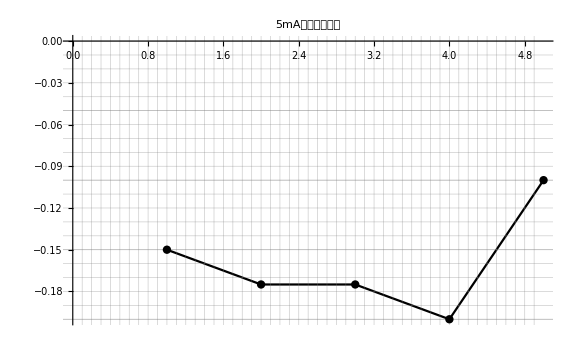

```mathematica
ListPlot[(#[[1]]*5-#[[2]])&/@list1,Joined->True,PlotStyle->Black,ImageSize->Large,Mesh->All,PlotLabel->Style["5mA电流表误差图",Black,20],GridLines->{Join[Table[i,{i,0,5,0.1}],Table[{i,Thick},{i,0,5,1}]],Join[Table[i,{i,-0.2,0,0.01}],Table[{i,Thick},{i,-0.2,0,0.05}]]},AxesLabel->MaTeX[{"Serial No.","\Delta I/mA"},Magnification->1.25]]
```

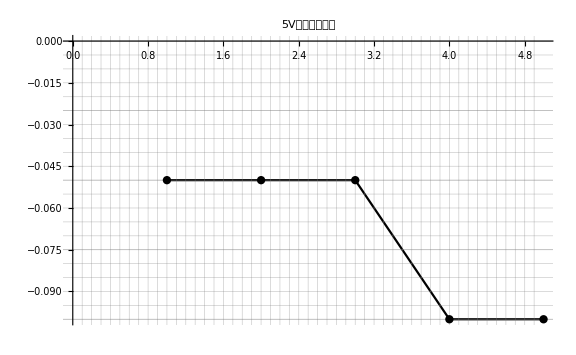

```mathematica
ListPlot[(#[[1]]*5-#[[2]])&/@list2,Joined->True,PlotStyle->Black,ImageSize->Large,Mesh->All,PlotLabel->Style["5V电压表误差图",Black,20],GridLines->{Join[Table[i,{i,0,5,0.1}],Table[{i,Thick},{i,0,5,1}]],Join[Table[i,{i,-0.2,0,0.005}],Table[{i,Thick},{i,-0.2,0,0.025}]]},AxesLabel->MaTeX[{"Serial No.","\Delta U/V"},Magnification->1.25]]
```

```mathematica
FindFit[list3,a/(b+x),{a,b},x]
```

{a→252.923,b→250.746}

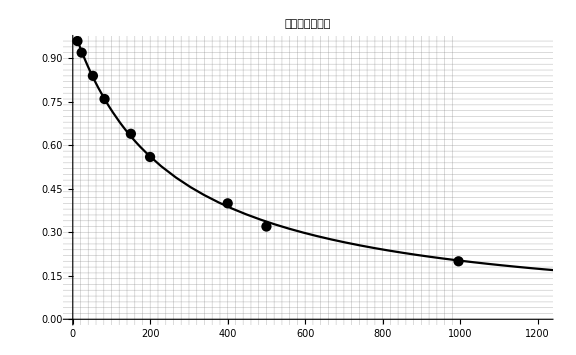

```mathematica
Show[ListPlot[list3,PlotStyle->Black,GridLines->{Join[Table[i,{i,0,1200,20}],Table[{i,Thick},{i,0,1200,200}]],Join[Table[i,{i,0,1,0.02}],Table[{i,Thick},{i,0,1,0.2}]]},AxesLabel->MaTeX[{"R/\Omega","A_g/mA"},Magnification->1.25],PlotLabel->Style["欧姆挡刻度曲线",20,Black]],Plot[a/(b+x)/.{a->252.92289724135117,b->250.74630143527287},{x,12,1800},PlotStyle->Black],ImageSize->Large]
```

```mathematica
Reduce[(R1+R2)(i-Ig)==Rg*Ig,i]
```

(Rg==0&&R1==-R2)||(R1+R2≠0&&i==(Ig (R1+R2+Rg))/(R1+R2))||(R1==-R2&&Rg≠0&&Ig==0)

```mathematica
(Ig (R1+R2+Rg))/(R1+R2)/.{R1->29,R2->29,Rg->229,Ig->1}
```

287/58

```mathematica
N@287/58
```

4.94828

```mathematica
TableForm[MaTeX/@{#[[1]],(#[[1]]*287/58)~SetPrecision~3,(#[[2]])~SetAccuracy~4,(#[[2]]-#[[1]]*287/58)~SetAccuracy~3,(#[[2]]-#[[1]]*5)~SetAccuracy~3}&/@list1,TableDirections->Row,TableHeadings->{MaTeX/@Range[5],MaTeX/@{"A_g/mA","A_{exp}/mA","A_{st}/mA","\Delta I/mA"}}]
```

| -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### 第四次

```mathematica
<<MaTeX`
```

```mathematica
list1={{18.1,0.008423},{25.1,0.008644},{30.4,0.008845},{42.9,0.009300},{45.1,0.009384},{50.1,0.009574},{55.2,0.009765},{60.0,0.009944},{65.1,0.010125},{70.1,0.010256},{74.6,0.010443},{80.0,0.010643},{85.2,0.010827},{90.1,0.011000}};
list2={{86.8,0.010880},{84.9,0.010800},{79.7,0.010605},{74.6,0.010414},{69.5,0.010230},{64.5,0.010050},{59.9,0.009884},{54.9,0.009701},{49.5,0.009520}};
list3={{20.5,0.000459},{17.0,0.000375},{13.0,0.000286},{10.0,0.000220},{6.00,0.000138},{3.50,0.000084}};
d=0.9-5/50*4.9;
```

```mathematica
d
```

0.41

```mathematica
Row[{TableForm[{SetAccuracy[#[[1]],2],SetAccuracy[#[[2]],7]}&/@list1,TableDirections->Column,TableHeadings->{None,MaTeX/@{"T_{Heating}/^oC","R_{Heating} /\Omega"}}], , , , , ,, , , , , ,  , , , TableForm[{SetAccuracy[#[[1]],2],SetAccuracy[#[[2]],7]}&/@list2,TableDirections->Column,TableHeadings->{None,MaTeX/@{"T_{Cooling}/^oC","R_{Cooling} /\Omega"}}]}]
TableForm[{SetAccuracy[#[[1]],3],SetAccuracy[#[[2]],7],SetPrecision[#[[2]]*Pi*d^2/400/#[[1]],3]}&/@list3,TableDirections->Column,TableHeadings->{None,{MaTeX@"L/cm",MaTeX@"R/\Omega",MaTeX[ρ]}}]
```

-Graphics- | -Graphics-
18.1 | 0.008423
25.1 | 0.008644
30.4 | 0.008845
42.9 | 0.0093
45.1 | 0.009384
50.1 | 0.009574
55.2 | 0.009765
60. | 0.009944
65.1 | 0.010125
70.1 | 0.010256
74.6 | 0.010443
80. | 0.010643
85.2 | 0.010827
90.1 | 0.011-Graphics- | -Graphics-
86.8 | 0.01088
84.9 | 0.0108
79.7 | 0.010605
74.6 | 0.010414
69.5 | 0.01023
64.5 | 0.01005
59.9 | 0.009884
54.9 | 0.009701
49.5 | 0.00952

-Graphics- | -Graphics- | -Graphics-
20.5 | 0.000459 | 2.96×10^-8
17. | 0.000375 | 2.91×10^-8
13. | 0.000286 | 2.9×10^-8
10. | 0.00022 | 2.9×10^-8
6. | 0.000138 | 3.04×10^-8
3.5 | 0.000084 | 3.17×10^-8

```mathematica
Mean[SetPrecision[#[[2]]*Pi*d^2/400/#[[1]],3]&/@list3]
SetAccuracy[StandardUncertaintyA[SetPrecision[#[[2]]*Pi*d^2/400/#[[1]],3]&/@list3],11]
SetAccuracy[StandardUncertaintyA[SetPrecision[#[[2]]*Pi*d^2/400/#[[1]],3]&/@list3],11]/Mean[SetPrecision[#[[2]]*Pi*d^2/400/#[[1]],3]&/@list3]
```

2.98×10^-8

5.×10^-10

0.02

```mathematica
{a,b,c}=Normal@LinearModelFit[#,x,x]&/@{list1,list2,list3}
{a1,b1}=Normal@LinearModelFit[#,Table[x^i,{i,1,3}],x]&/@{list1,list2}
```

{0.00775999+0.0000360267 x,0.0077019+0.0000364679 x,0.000517989+6.20095×10^-6 x}

{0.00777537+0.0000342968 x+4.63229×10^-8 x^2-3.38076×10^-10 x^3,0.00779469+0.0000359554 x-4.72053×10^-8 x^2+4.84367×10^-10 x^3}

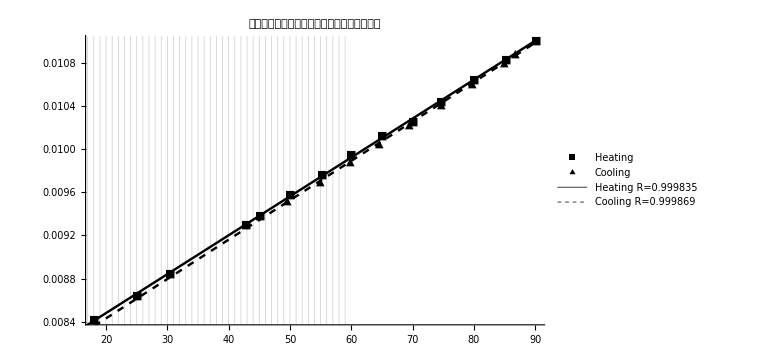

```mathematica
Show[ListPlot[{list1,list2},Joined->False,PlotStyle->Black,ImageSize->Large,Mesh->All,PlotLabel->Style["金属导体电阻随温度变化关系图（线性拟合）",Black,20],GridLines->{Join[Table[i,{i,10,100,1}],Table[{i,Thick},{i,10,90,10}]],Join[Table[i,{i,0,0.1,0.00005}],Table[{i,Thick},{i,0,0.1,0.0005}]]},AxesLabel->MaTeX[{"T/^oC","R/\Omega"},Magnification->1.25],PlotMarkers->{"■","▲"},PlotLegends->{"Heating","Cooling"}],Plot[{a,b},{x,0,90},PlotStyle->{{Black,Thickness[0.003]},{Black,Dashed,Thickness[0.003]}},PlotLegends->{StringJoin["Heating","\n","R=",ToString[r[list1]],"\n"],StringJoin["Cooling","\n","R=",ToString[r[list2]],"\n"]}]]
```

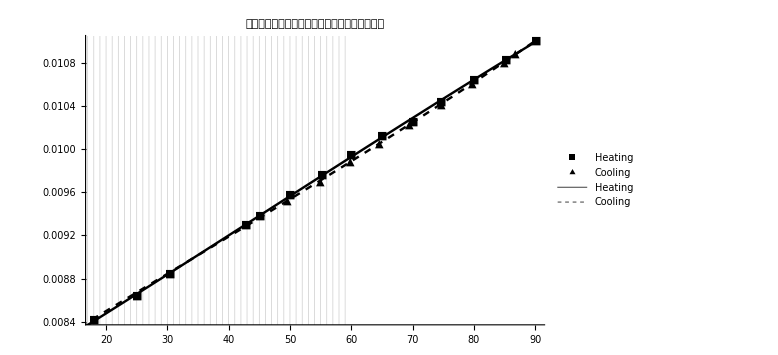

```mathematica
Show[ListPlot[{list1,list2},Joined->False,PlotStyle->Black,ImageSize->Large,Mesh->All,PlotLabel->Style["金属导体电阻随温度变化关系图（非线性拟合）",Black,20],GridLines->{Join[Table[i,{i,10,100,1}],Table[{i,Thick},{i,10,90,10}]],Join[Table[i,{i,0,0.1,0.00005}],Table[{i,Thick},{i,0,0.1,0.0005}]]},AxesLabel->MaTeX[{"T/^oC","R/\Omega"},Magnification->1.25],PlotMarkers->{"■","▲"},PlotLegends->{"Heating","Cooling"}],Plot[{a1,b1},{x,0,90},PlotStyle->{{Black,Thickness[0.003]},{Black,Dashed,Thickness[0.003]}},PlotLegends->{"Heating","Cooling"}]]
```

#### 第五次

```mathematica
<<MaTeX`
```

```mathematica
list1={{60.0,10.6},{65.0,15.8},{70.0,21.1},{75.0,26.3},{80.0,31.3},{83.7,34.9},{85.0,36.2},{87.8,38.9},{90.0,41.1},{92.6,43.7},{95.1,46.1},{98.9,49.8},{100.0,50.8},{105.0,55.5}}~SetAccuracy~2;
list2={{100.0,50.9},{94.9,46.2},{90.0,41.3},{84.6,38.1},{79.8,32.6},{73.7,25.7},{70.0,22.0},{64.3,15.8},{60.0,11.2}}~SetAccuracy~2;
list3={SetAccuracy[#[[1]],2],SetAccuracy[#[[2]],3]}&/@{{57.0,63.08},{63.6,64.45},{67.8,65.35},{71.1,66.05},{74.5,66.69},{75.9,66.99},{79.1,67.70},{84.9,68.90},{87.9,69.60},{89.8,70.00},{91.6,70.40},{93.9,70.90},{96.7,71.50},{98.1,71.80},{99.1,72.00},{103.7,73.00}};
```

```mathematica
TableForm[MaTeX/@
(Flatten/@Transpose[{Flatten/@Transpose[{PadRight[list1,{16,2},{"",""}],PadRight[list2,{16,2},{"",""}]}],list3}]),TableHeadings->{MaTeX/@Range[16],MaTeX/@{"T_{Heating}/^o C","U_{Heating}/mV","T_{Cooling}/^o C","U_{Cooling}/mV","T_{Wheatstone}/^o C","R/ \Omega"}}]
```

| -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
lista=(a/.Solve[U==(R2*R0*(1+a*(T-50))-R1*R3)/((R1+R0(1+a*(T-50)))(R2+R3))*Ε/.{R1->50,R2->50,R3->60.71,R0->60.71,U->#2/1000,T->#1,Ε->1.3},a]&@@@list1//Quiet//Flatten)~SetPrecision~3;
listb=(a/.Solve[U==(R2*R0*(1+a*(T-50))-R1*R3)/((R1+R0(1+a*(T-50)))(R2+R3))*Ε/.{R1->50,R2->50,R3->60.71,R0->60.71,U->#2/1000,T->#1,Ε->1.3},a]&@@@list2//Quiet//Flatten)~SetPrecision~3;
```

```mathematica
TableForm[MaTeX/@Flatten/@Transpose[{lista,PadRight[listb,Length[lista],""]}],TableHeadings->{MaTeX/@Range[14],MaTeX/@{"\alpha_{Heating}","\alpha_{Cooling}"}}]
```

| -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Mean@#&/@{lista,listb}
```

{0.00342,0.00353}

```mathematica
((Abs[#-0.004280]/0.004280&)/@(Mean@#&/@{lista,listb}))~SetPrecision~3
```

{0.2,0.175}

```mathematica
SetAccuracy[StandardUncertaintyA[#],6]&/@{lista,listb}
```

{9.×10^-6,0.00002}

```mathematica
SetPrecision[StandardUncertaintyA[#]/Mean[#],3]&/@{lista,listb}
```

{0.00264,0.00671}

```mathematica
line1=FindFit[list1,(a*t-b)/(c*t-d),{a,b,c,d},t]
line2=FindFit[list2,(a*t-b)/(c*t-d),{a,b,c,d},t]//Quiet
```

{a→2570.,b→128000.,c→1.72,d→-2370.}

{a→145.,b→7430.,c→0.569,d→-80.8}

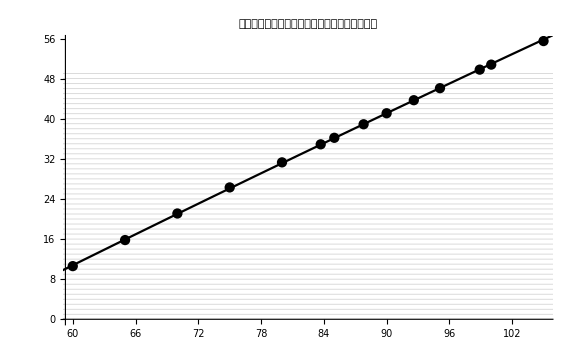

```mathematica
Show[ListPlot[list1,Joined->False,AxesLabel->MaTeX[{"T/^oC","U/mV"},Magnification->1.25],GridLines->{Join[Table[i,{i,10,200,1}],Table[{i,Thick},{i,10,200,5}]],Join[Table[i,{i,0,100,1}],Table[{i,Thick},{i,0,100,10}]]},PlotStyle->Black,PlotLabel->Style["非平衡电桥测得电压随温度变化关系图（升温）",18,Black]],
Plot[(a*t-b)/(c*t-d)/.line1,{t,0,200},PlotStyle->Black,PlotLegends->(U==(a*t-b)/(c*t-d)/.Join[line1,{t->T}])],ImageSize->Large]
```

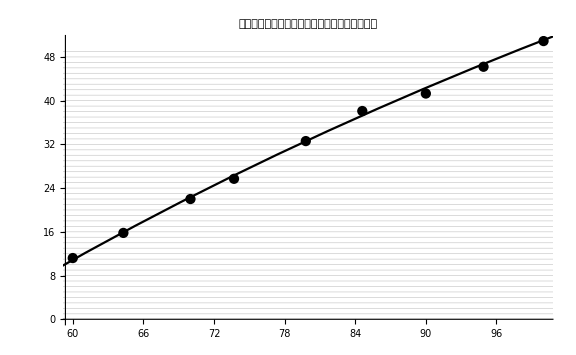

```mathematica
Show[ListPlot[list2,Joined->False,AxesLabel->MaTeX[{"T/^oC","U/mV"},Magnification->1.25],GridLines->{Join[Table[i,{i,10,200,1}],Table[{i,Thick},{i,10,200,5}]],Join[Table[i,{i,0,100,1}],Table[{i,Thick},{i,0,100,10}]]},PlotStyle->Black,PlotLabel->Style["非平衡电桥测得电压随温度变化关系图（降温）",18,Black]],
Plot[(a*t-b)/(c*t-d)/.line2,{t,0,200},PlotStyle->Black,PlotLegends->(U==(a*t-b)/(c*t-d)/.Join[line2,{t->T}])],ImageSize->Large]
```

```mathematica
line3=SetPrecision[Fit[list3,{1,x},x],3]
```

50.9+0.213 x

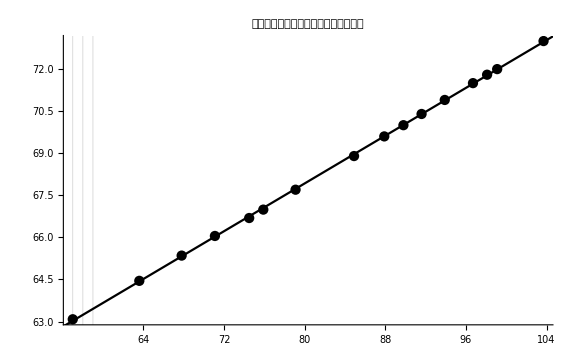

```mathematica
Show[ListPlot[list3,Joined->False,AxesLabel->MaTeX[{"T/^oC","R/\Omega"},Magnification->1.25],GridLines->{Join[Table[i,{i,10,200,1}],Table[{i,Thick},{i,10,200,5}]],Join[Table[i,{i,0,100,0.2}],Table[{i,Thick},{i,0,100,1}]]},PlotStyle->Black,PlotLabel->Style["惠斯登电桥测得电阻随温度变化关系图",18,Black]],
Plot[line3,{x,0,200},PlotStyle->Black,PlotLegends->StringJoin["R=",ToString[line3/.x->T],"\n\n","R=",ToString[SetAccuracy[r[list1],8]],"\n"]],ImageSize->Large]
```

```mathematica
(0.213/60.70)~SetPrecision~3
```

0.00351

```mathematica
(0.004280-0.00351)/0.004280
```

0.179907

#### 第六次

```mathematica
<<MaTeX`
```

```mathematica
lista={{69199.4,6.8,1000,1.1},{68009.4,6.8,1000,1.1},{67809.4,6.8,1000,1.0},{67500.4,6.8,1000,1.1},{67090.0,6.8,1000,1.2},{67800.4,6.8,1000,1.0},{67389.5,6.8,1000,1.0},{68439.3,6.8,1000,1.0}};
listb={{6911,10,5.0},{6801,10,5.0},{6765,10,5.5},{6768,10,5.0},{6730,10,5.0},{6792,10,5.0},{6764,10,5.0},{6870,10,5.0}};
```

```mathematica
TableForm[MaTeX/@{#1~SetPrecision~6,#2~SetPrecision~2,#3~SetPrecision~5,#4~SetPrecision~2,Sqrt[#1*#2]~SetPrecision~6,#4/(#3/#1)~SetAccuracy~1,Sqrt[(0.001+(0.002*6)/#1)^2+(0.2/(#4/(#3/#1)))^2]}&@@@lista,TableHeadings->{None,MaTeX/@{"R_s /\Omega","R_s'/\Omega","\Delta R_s/\Omega","d","R_x/\Omega","S","E"}}]
TableForm[MaTeX/@{#1~SetPrecision~4,#2,#3~SetPrecision~2,(#1/10)~SetPrecision~4,#3/(#2/#1)~SetAccuracy~1,Sqrt[(0.001+(0.002*4)/#1)^2+(0.2/(#3/(#2/#1)))^2]~SetPrecision~6}&@@@listb,TableHeadings->{None,MaTeX/@{"R_s /\Omega","\Delta R_s/\Omega","d","R_x/\Omega","S","E"}}]
TableForm[MaTeX/@{{#1~SetPrecision~6,#2,#3~SetPrecision~2,(#1/100)~SetPrecision~4,#3/(#2/#1)~SetAccuracy~1,Sqrt[(0.001+(0.002*4)/#1)^2+(0.2/(#3/(#2/#1)))^2]~SetPrecision~6}&@@{22000.0,100,0.9},{#1~SetPrecision~4,#2,#3~SetPrecision~2,(#1/10)~SetPrecision~4,#3/(#2/#1)~SetAccuracy~1,Sqrt[(0.001+(0.002*4)/#1)^2+(0.2/(#3/(#2/#1)))^2]~SetPrecision~6}&@@{2205,1,4.0~SetPrecision~2}},TableHeadings->{MaTeX/@{"Self-made","Order-made"},MaTeX/@{"R_s /\Omega","\Delta R_s/\Omega","d","R_x/\Omega","S","E"}}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

| -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Variance@(Flatten@(Take[#,1]&/@lista)/100)
N@Variance[Flatten@(Take[#,1]&/@listb/10)]
```

44.0799

36.7584

#### 第七次

```mathematica
<<MaTeX`
```

```mathematica
list={#1~SetPrecision~3,#2~SetPrecision~3,(#2/(2*Pi*19.65))~SetPrecision~3*1000}&@@@{{23.4,6.73},{39.7,6.44},{43.1,5.72},{53.3,5.15},{64.7,4.92},{67.0,4.63},{69.8,4.52},{73.6,4.40},{78.6,4.35},{85.2,4.50},{90.7,4.48}};
TableForm[MaTeX/@list,TableHeadings->{MaTeX/@Range[Length[list]],MaTeX/@{"T/^oC","F/mN","\delta/10^{-3}N/m"}}]
```

| -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
list2={{10,74.22},{20,72.75},{25,71.97},{30,71.18},{35,70.38},{40,69.56},{45,68.74}};
```

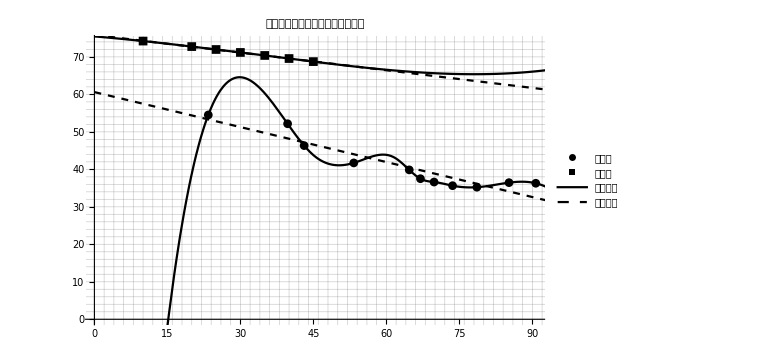

```mathematica
Show[ListPlot[{{#1,#3}&@@@list,list2},PlotMarkers->Automatic,PlotStyle->Black,PlotLegends->{"实验值","理论值"},GridLines->{Join[Table[i,{i,0,100,2}],Table[{i,Thick},{i,0,100,10}]],Join[Table[i,{i,0,100,2}],Table[{i,Thick},{i,0,100,10}]]},AxesLabel->MaTeX/@{"T/^oC","\delta /(10^{-3}N/m)"}],
Plot[{Interpolation[list2,Method->"Spline"][x],
Evaluate[Fit[list2,{1,x},x]],Interpolation[{#1,#3}&@@@list,Method->"Spline"][x],Evaluate[Fit[{#1,#3}&@@@list,{1,x},x]]},{x,0,100},PlotStyle->{Black,{Black,Dashed},Black,{Black,Dashed}},PlotLegends->{"插值拟合","线性拟合"}],ImageSize->Large,PlotLabel->Style["水表面张力系数随温度变化曲线图",20]]
```

#### 第八次

```mathematica
<<MaTeX`
```

```mathematica
TableForm[MaTeX/@(list={#1,#2~SetAccuracy~4,2*#3~SetAccuracy~2,#4~SetPrecision~3,(#4/(2*#2*#3))~SetPrecision~3}&@@@Flatten/@Transpose[{Table[i,{i,0,9}],{{0.338,112.0,27.3},{0.277,112.0,27.3},{0.234,112.0,29.0},{0.181,112.0,28.8},{0.161,112.0,30.0},{0.144,112.2,30.0},{0.146,112.5,30.2},{0.145,112.5,30.5},{0.154,112.5,30.2},{0.190,112.5,30.5}}}]),TableHeadings->{None,MaTeX/@{"C/\mu F","I/A","U/V","P/W","cos \phi"}}]//Quiet
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

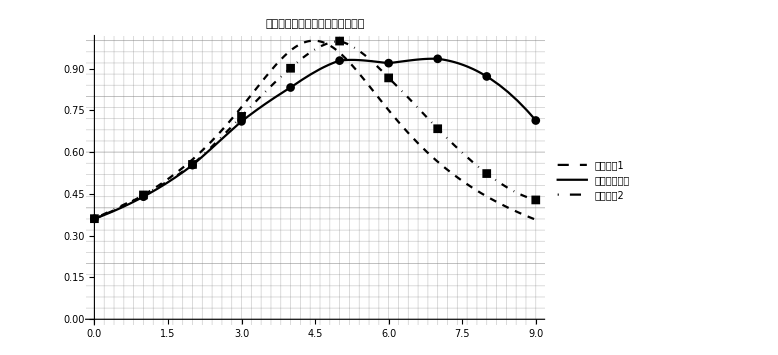

```mathematica
f[U_,P_,cosϕ_,c_]:=Cos[ArcTan[(Tan[ArcCos[cosϕ]]-2Pi*10^-6*c*50*U^2/P)]];
Show[ListPlot[{{#1,#5}&@@@list,{#3,f[#1,#2,0.361,#3]}&@@@({#3,#4,#1}&@@@list)},PlotStyle->Black,PlotRange->All,PlotMarkers->Automatic,GridLines->{Join[Table[i,{i,0,10,0.2}],Table[{i,Thick},{i,0,10,1}]],Join[Table[i,{i,0,1,0.04}],Table[{i,Thick},{i,0,1,0.2}]]},AxesLabel->MaTeX/@{"C/\mu F","cos \phi"},PlotLabel->Style["功率因数关于电容大小变化曲线图",18,Black]],Plot[{f[224,27.3,0.361,c],Interpolation[{#1,#5}&@@@list][c],Interpolation[{#3,f[#1,#2,0.361,#3]}&@@@({#3,#4,#1}&@@@list)][c]},{c,0,9},PlotStyle->{{Dashed,Black},Black,{DotDashed,Black}},PlotLegends->{"理论曲线1","实验值及曲线","理论曲线2"}],ImageSize->Large]
```

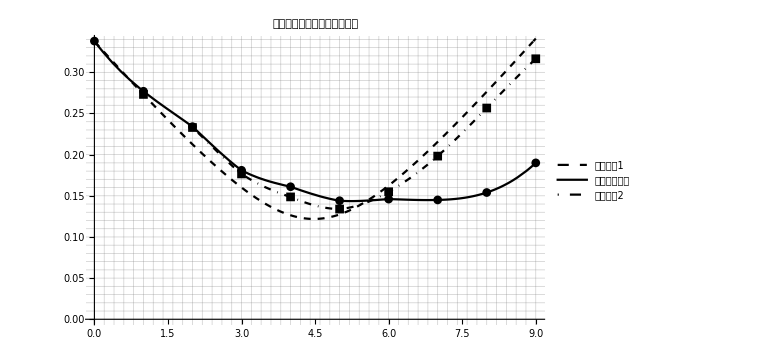

```mathematica
g[U_,P_,cosϕ_,c_]:=P/U(Tan[ArcCos[cosϕ]]-Tan@ArcCos[f[U,P,cosϕ,c]]);
h[U_,P_,cosϕ_,c_]:=g[U,P,cosϕ,c]/Sin@(ArcCos[cosϕ]-ArcCos[f[U,P,cosϕ,c]])*cosϕ;
Show[ListPlot[{{#1,#2}&@@@list,{#3,h[#1,#2,0.361,#3]}&@@@({#3,#4,#1}&@@@list)},PlotStyle->Black,PlotRange->All,PlotMarkers->Automatic,GridLines->{Join[Table[i,{i,0,10,0.2}],Table[{i,Thick},{i,0,10,1}]],Join[Table[i,{i,0,1,0.01}],Table[{i,Thick},{i,0,1,0.05}]]},AxesLabel->MaTeX/@{"C/\mu F","I/A"},PlotLabel->Style["电流关于电容大小变化曲线图",18,Black]],Plot[{h[224,27.3,0.361,c],Interpolation[{#1,#2}&@@@list][c],Interpolation[{#3,h[#1,#2,0.361,#3]}&@@@({#3,#4,#1}&@@@list)][c]},{c,0,9},PlotStyle->{{Dashed,Black},Black,{DotDashed,Black}},PlotLegends->{"理论曲线1","实验值及曲线","理论曲线2"}],ImageSize->Large]//Quiet
```

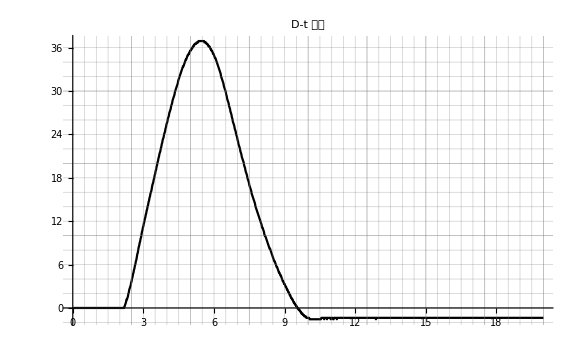

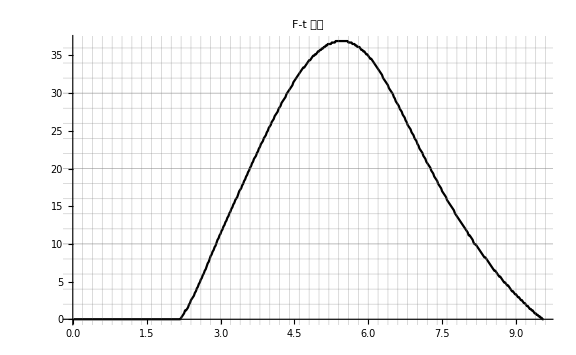

```mathematica
<<MaTeX`
list=ToExpression@Flatten@StringSplit@Import["/Users/Apple/Documents/233.txt","List"];
list1=Transpose[{Table[i/50,{i,Length[Select[list,#≥59&]]}],Select[list,#≥59&]}];
list2={#1,10*5/256*(#2-59)}&@@@list1;
list3=Transpose[{Table[i/50,{i,Length[list]}],list}];
list4={#1,10*5/256*(#2-59)}&@@@list3;
ListPlot[list4,Joined->True,AxesLabel->MaTeX/@{Style["t/ms",Black,15],Style["D",Black,15]},
GridLines->{Join[Table[i,{i,0,20,0.5}],Table[{i,Thick},{i,0,20,2.5}]],Join[Table[i,{i,-10,50,2}],Table[{i,Thick},{i,0,50,10}]]},
PlotLabel->Style["D-t 图像",Black,20],ImageSize->Large,PlotStyle->Black]
ListPlot[list2,Joined->True,AxesLabel->MaTeX/@{Style["t/ms",Black,15],Style["F/N",Black,15]},
GridLines->{Join[Table[i,{i,0,20,0.2}],Table[{i,Thick},{i,0,20,1}]],Join[Table[i,{i,-10,50,2}],Table[{i,Thick},{i,0,50,10}]]},
PlotLabel->Style["F-t 图像",Black,20],ImageSize->Large,PlotStyle->Black]
```

```mathematica
N@Total[2*10^-5*#2&@@@list2]
```

0.145332

```mathematica
0.16500*(10/15.19+10/24.82)
```

0.175103

```mathematica
listtem=Select[list2,Last@#>0&];
Length@listtem
```

367

```mathematica
225*20/(1/30*4.00)*1/2^8
```

131.836